# Bulge To Spike

If I have a Hessenberg matrix with a bulge in it. I can transform the bulge to a “spike” form using a small orthogonal matrix Q.

### Hessenberg Decomposition

The Hessenberg decomposition decomposition of a matrix is the first step in dense eigenvalue decompositions. It uses orthogonal matrices to generate an eigenvalue equivalent “almost” upper triangular matrix.  There is only one Hessenberg decomposition with all positive sub-diagonals. Built in commands do not care about the sign of the subdiagonal.  If you allow negatives in the sub-diagonal the Hessenberg decomposition is not unique.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
{Q,H}=HessenbergDecomposition[A];
TabView[{
"A"->MatrixPlot[A],
"H"->MatrixPlot[H],
"Qᵀ.A.Q"->MatrixPlot[Qᵀ.A.Q]
},2]
```

123

For a symmetric matrix the result is symmetric tridiagonal.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
{Q,H}=HessenbergDecomposition[A];
TabView[{
"A"->MatrixPlot[A],
"H"->MatrixPlot[H],
"Qᵀ.A.Q"->MatrixPlot[Qᵀ.A.Q]
},2]
```

123

### SchurDecomposition

The Schur decomposition of a matrix is essentially a eigenvalue decomposition except it forces orthogonal transformations. As a result of the orthogonality constraint, it can not go all the way to diagonal. A Schur decomposition goes to essentially upper triangular.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
{Q,T}=SchurDecomposition[A];
TabView[{
"A"->MatrixPlot[A],
"T"->MatrixPlot[T],
"Qᵀ.A.Q"->MatrixPlot[Qᵀ.A.Q]
},2]
```

123

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A= A+ Aᵀ;
{Q,T}=SchurDecomposition[A];
TabView[{
"A"->MatrixPlot[A],
"T"->MatrixPlot[T],
"Qᵀ.A.Q"->MatrixPlot[Qᵀ.A.Q]
},2]
```

123

### Bulge to Spike: Top

I can use the Schur decomposition of the bulge to reduce a bulge on a Hessenberg matrix to a spike form. If the block is at the top.  I get a single spike at the top. If the start of the spike is zero then I can identify eigenvalues in the matrix.

```mathematica
{m,b}={54,8};
SetOptions[MatrixPlot,ColorRules->{0->LightGreen}];
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
H⟦1;;b,1;;b⟧=RandomReal[{-1,1},{b,b}];
B=H⟦1;;b,1;;b⟧;
{Q,T}=SchurDecomposition[B];
BigQ=IdentityMatrix[m]; 
BigQ⟦1;;b,1;;b⟧=Q;
Spike=Chop[BigQᵀ.H.BigQ];
TabView[{
"H"->MatrixPlot[Chop[H],Mesh->{{1,b},{1,b}}],
"QᵀBQ"->MatrixPlot[Chop[Qᵀ.B.Q]],
"BigQ"->MatrixPlot[Chop[BigQ]],
"BigQᵀHBigQ"->MatrixPlot[Spike,Mesh->{{1,b},{1,b}}]
}]
```

1234

### Bulge to Spike: Bottom

I can use the Schur decomposition of the bulge to reduce a bulge on a Hessenberg matrix to a spike form. If the block is at the bottom.  I get a single spike at the bottom. If the bottom of the spike is zero then I can identify eigenvalues in the matrix.

```mathematica
{m,b}={54,8};
SetOptions[MatrixPlot,ColorRules->{0->LightGreen}];
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
H⟦m-b+1;;m,m-b+1;;m⟧=RandomReal[{-1,1},{b,b}];
B=H⟦m-b+1;;m,m-b+1;;m⟧;
{Q,T}=SchurDecomposition[B];
BigQ=IdentityMatrix[m]; 
BigQ⟦m-b+1;;m,m-b+1;;m⟧=Q;
Spike=Chop[BigQᵀ.H.BigQ];
TabView[{
"H"->MatrixPlot[Chop[H],Mesh->{{m,m-b},{m,m-b}}],
"QᵀBQ"->MatrixPlot[Chop[Qᵀ.B.Q]],
"BigQ"->MatrixPlot[Chop[BigQ]],
"BigQᵀHBigQ"->MatrixPlot[Spike,Mesh->{{m,m-b},{m,m-b}}]
}]
```

1234

### Bulge to Spike: Middle “Stable Footprint”

I can use the Schur decomposition of the bulge to reduce a bulge on a Hessenberg matrix to a spike form. If the block is in the middle.  I get a single spike at the bottom. If the far ends of the spike are zero then I can identify eigenvalues in the matrix. Here is an “inside” version of this trick.

```mathematica
{m,s,b}={56,24,14};
SetOptions[MatrixPlot,ColorRules->{0->LightGreen}];
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
H⟦s+1;;s+b,s+1;;s+b⟧=RandomReal[{-1,1},{b,b}];
B=H⟦s+2;;s+b-1,s+2;;s+b-1⟧;
{Q,T}=SchurDecomposition[B];
BigQ=IdentityMatrix[m]; 
BigQ⟦s+2;;s+b-1,s+2;;s+b-1⟧=Q;
Spike=Chop[BigQᵀ.H.BigQ];
TabView[{
"H"->MatrixPlot[Chop[H],Mesh->{{s,s+b},{s,s+b}}],
"QᵀBQ"->MatrixPlot[Chop[Qᵀ.B.Q]],
"BigQ"->MatrixPlot[Chop[BigQ],Mesh->{{s,s+b},{s,s+b}}],
"BigQᵀHBigQ"->MatrixPlot[Spike,Mesh->{{s,s+b},{s,s+b}}]
}]
```

1234

### Bulge to Spike: Middle “Expanded Footprint”

I can use the Schur decomposition of the bulge to reduce a bulge on a Hessenberg matrix to a spike form. If the block is in the middle.  I get a single spike at the bottom. If the far ends of the spike are zero then I can identify eigenvalues in the matrix. Here is an “outside” version of this trick. This one automatically has the outside corner entry zeroed.

```mathematica
{m,s,b}={56,24,14};
SetOptions[MatrixPlot,ColorRules->{0->LightGreen}];
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
H⟦s+1;;s+b,s+1;;s+b⟧=RandomReal[{-1,1},{b,b}];
B=H⟦s+1;;s+b,s+1;;s+b⟧;
{Q,T}=SchurDecomposition[B];
BigQ=IdentityMatrix[m]; 
BigQ⟦s+1;;s+b,s+1;;s+b⟧=Q;
Spike=Chop[BigQᵀ.H.BigQ];
TabView[{
"H"->MatrixPlot[Chop[H],Mesh->{{s,s+b},{s,s+b}}],
"QᵀBQ"->MatrixPlot[Chop[Qᵀ.B.Q]],
"BigQ"->MatrixPlot[Chop[BigQ],Mesh->{{s,s+b},{s,s+b}}],
"BigQᵀHBigQ"->MatrixPlot[Spike,Mesh->{{s,s+b},{s,s+b}}]
}]
```

1234

```mathematica
RandomChoice
```

RandomChoice

## Schur Sorting

#### Single Bulge

Just making sure we have the transposes in the correct places again and that I can build the spikes directly from the matrices.

123

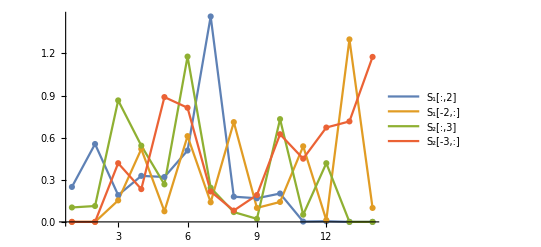

```mathematica
m=14;
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
Bulge=RandomReal[{-1,1},{m-4,m-4}];
H⟦3;;-3,3;;-3⟧=Bulge;
{Q1,T1}=SchurDecomposition[Bulge];
Q1Big=IdentityMatrix[m];Q1Big⟦3;;-3,3;;-3⟧=Q1;
{Q2,T2}=SchurDecomposition[Bulge⟦2;;-2,2;;-2⟧];
Q2Big=IdentityMatrix[m];Q2Big⟦4;;-4,4;;-4⟧=Q2;

TabView[{
"H"->MatrixPlot[Chop[H],ColorRules->{0->LightGreen},Mesh->All],
"Q1ᵀ.H.Q1"->MatrixPlot[S1=Chop[Q1Bigᵀ.H.Q1Big],ColorRules->{0->LightGreen},Mesh->All],
"Q2ᵀ.H.Q2"->MatrixPlot[S2=Chop[Q2Bigᵀ.H.Q2Big],ColorRules->{0->LightGreen},Mesh->All]
},2
]
(* s1V is the entire vertical spike column similarly s1H is horizontal spike row *)
ListPlot[{Abs[s1V=S1⟦All,2⟧],Abs[s1H=S1⟦-2,All⟧],Abs[s2V=S2⟦All,3⟧],Abs[s2H=S2⟦-3,All⟧]},
Joined->True,Mesh->All,PlotRange->All,
PlotLegends->{"S_1[:,2]","S_1[-2,:]","S_2[:,3]","S_2[-3,:]"}]
```

The matrix residuals all check out.

```mathematica
Map[Norm,
{Q1Bigᵀ.Q1Big-IdentityMatrix[m],Q2Bigᵀ.Q2Big-IdentityMatrix[m], S1-Q1Bigᵀ.H.Q1Big,S2-Q2Bigᵀ.H.Q2Big}]
```

{3.09939×10^-15,2.45414×10^-15,2.1868×10^-15,2.20534×10^-15}

I need to find/compute the spikes. Lots of the Q columns are identity columns.

```mathematica
{s1V,Join[H⟦1;;2,2⟧,Q1ᵀ.H⟦3;;-3,2⟧,H⟦-2;;-1,2⟧]}ᵀ
{s2V,Join[H⟦1;;3,3⟧,Q2ᵀ.H⟦4;;-4,3⟧,H⟦-3;;-1,3⟧]}ᵀ
```

{{-0.249116,-0.249116},{0.554861,0.554861},{-0.190714,-0.190714},{0.327862,0.327862},{0.319951,0.319951},{0.508484,0.508484},{-1.46351,-1.46351},{-0.179575,-0.179575},{0.16829,0.16829},{0.202067,0.202067},{-0.00236486,-0.00236486},{0.00474667,0.00474667},{0,0.},{0,0.}}

{{-0.102864,-0.102864},{-0.113159,-0.113159},{-0.865591,-0.865591},{-0.543204,-0.543204},{0.267279,0.267279},{1.17777,1.17777},{-0.243094,-0.243094},{-0.0699835,-0.0699835},{-0.0217521,-0.0217521},{-0.732161,-0.732161},{-0.0513648,-0.0513648},{-0.41811,-0.41811},{0,0.},{0,0.}}

I can permute the entries in the Qs.  I can not move the other entries.

```mathematica
H⟦All,3⟧
```

{-0.102864,-0.113159,-0.865591,-0.585878,0.812528,0.785135,-0.407944,-0.364871,0.327241,0.286406,-0.498257,-0.41811,0.,0.}

```mathematica
Map[Dimensions,{Q1,Q2ᵀH⟦4;;-4,3⟧}]
```

{{10,10},{8,8},{8}}

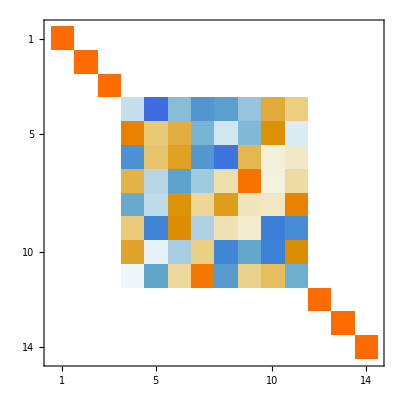

{-0.102864,-0.113159,-0.865591,-0.585878,0.812528,0.785135,-0.407944,-0.364871,0.327241,0.286406,-0.498257,-0.41811,0.,0.}

```mathematica
MatrixPlot[Q2Bigᵀ]
H⟦All,3⟧
```

```mathematica
Q1Big⟦All,2⟧
```

{0,1,0,0,0,0,0,0,0,0,0,0,0,0}

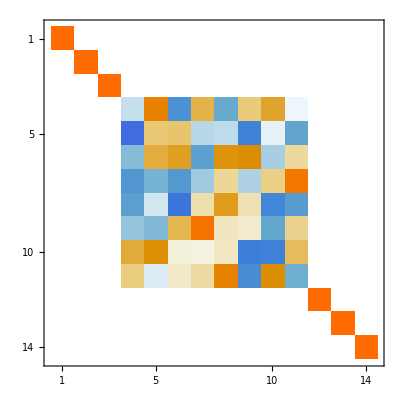

```mathematica
MatrixPlot[Q2Big]
```

#### Sorting a single bulge is simple.

I do the Schur transpose look at the output and simply pretend I have pre pivoted the input bulge.  Doing the big one first.

```mathematica
m=14;
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
Bulge=RandomReal[{-1,1},{m-4,m-4}];
H⟦3;;-3,3;;-3⟧=Bulge;
{Q1,T1}=SchurDecomposition[Bulge];
Q1Big=IdentityMatrix[m];Q1Big⟦3;;-3,3;;-3⟧=Q1;
{Q2,T2}=SchurDecomposition[Bulge⟦2;;-2,2;;-2⟧];
Q2Big=IdentityMatrix[m];Q2Big⟦4;;-4,4;;-4⟧=Q2;

TabView[{
"H"->MatrixPlot[Chop[H],ColorRules->{0->LightGreen},Mesh->All],
"Q1ᵀ.H.Q1"->MatrixPlot[S1=Chop[Q1Bigᵀ.H.Q1Big],ColorRules->{0->LightGreen},Mesh->All],
"Q2ᵀ.H.Q2"->MatrixPlot[S2=Chop[Q2Bigᵀ.H.Q2Big],ColorRules->{0->LightGreen},Mesh->All]
},2
]
ListPlot[{Abs[S1⟦All,2⟧],Abs[S1⟦-2,All⟧],Abs[S2⟦All,3⟧],Abs[S2⟦-3,All⟧]},
Joined->True,Mesh->All,PlotRange->All,
PlotLegends->{"S_1[:,2]","S_1[-2,:]","S_2[:,3]","S_2[-3,:]"}]
```

```mathematica
S1⟦All,2⟧
S1⟦2,All⟧
```

{-0.809938,-0.174532,-0.0224917,-0.8029,0.144908,-0.38058,0.670884,0.541217,-0.429989,-0.505067,-1.36204,0.0385669,0,0}

{-1.99544,-0.174532,-0.525525,0.849921,0.206564,0.00776604,-0.457059,0.78493,0.150761,0.134729,-0.944074,-0.0387251,-0.375186,-0.624473}